```mathematica
f[x_]:=InterpolatingPolynomial[{{0,1,0},{1,0,-0.7}},x]
```

```mathematica
ColorData[1,"ColorList"]
```

{RGBColor[0.2472,0.24,0.6],RGBColor[0.6,0.24,0.442893],RGBColor[0.6,0.547014,0.24],RGBColor[0.24,0.6,0.33692],RGBColor[0.24,0.353173,0.6],RGBColor[0.6,0.24,0.563266],RGBColor[0.6,0.426641,0.24],RGBColor[0.263452,0.6,0.24],RGBColor[0.24,0.473545,0.6],RGBColor[0.516361,0.24,0.6],RGBColor[0.6,0.306268,0.24],RGBColor[0.383825,0.6,0.24],RGBColor[0.24,0.593918,0.6],RGBColor[0.395989,0.24,0.6],RGBColor[0.6,0.24,0.294104]}

```mathematica
red=ColorData[1,"ColorList"][[2]];
blue =ColorData[1,"ColorList"][[1]];
```

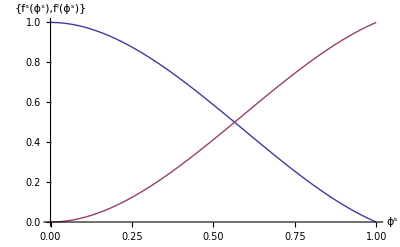

```mathematica
p=Plot[{f[x],1-f[x]},{x,0,1},AxesLabel->{ϕ^s,{Text[Style["f^s(ϕ^s)",red]],Text[Style["f^l(ϕ^s)",blue]]}}]
```

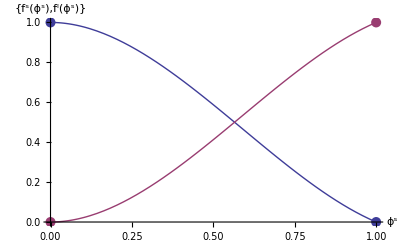

```mathematica
Show[p,ListPlot[{ {{0,1},{1,0}}, {{0,0},{1,1}} },PlotStyle->PointSize[0.018]]]
```

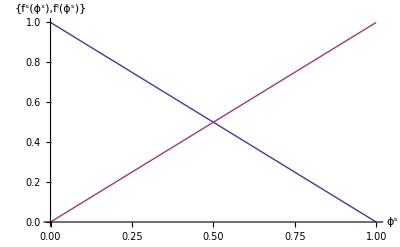

```mathematica
p2=Plot[{1-x,x},{x,0,1},AxesLabel->{ϕ^s,{Text[Style["f^s(ϕ^s)",red]],Text[Style["f^l(ϕ^s)",blue]]}}]
```

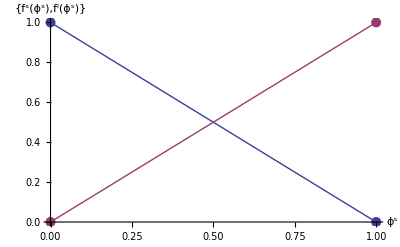

```mathematica
Show[p2,ListPlot[{ {{0,1},{1,0}}, {{0,0},{1,1}} },PlotStyle->PointSize[0.018]]]
```